```mathematica
y[x_]:=√x
z [x_]:=x^2
RevolutionPlot3D[{{y[t]},{z[t]}},{t,0,1},RevolutionAxis->"x",Boxed->True,Axes->True]
Export["thing.stl", %]
```

-Graphics3D-

thing.stl

```mathematica
RevolutionPlot3D[Sin[t]+2,{t,0,2Pi},{d,0,2Pi},RevolutionAxis->"x"]
```

-Graphics3D-

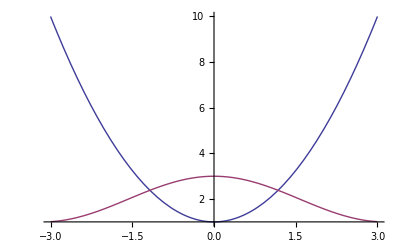

-Graphics3D-

```mathematica
y[x_]:=x^2 + 1
z [x_]:=Cos[x]+2
Plot[{{y[x]},{z[x]}},{x,-3,3}]

RevolutionPlot3D[{{y[t]},{z[t]}},{t,-1.177,1.177}, RevolutionAxis->"x",Boxed->True,Axes->True]
```

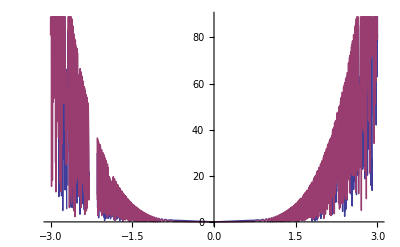

-Graphics3D-

```mathematica
y[x_]:=Sqrt[x^2+x^9Sin[8Pi x^5]]
z [x_]:=Sqrt[x^8+x^9Sin[8Pi x^5]]
Plot[{{y[x]},{z[x]}},{x,-3,3}]

RevolutionPlot3D[{{y[t]},{z[t]}},{t,0,1}, RevolutionAxis->"x",Boxed->True,Axes->True]
```

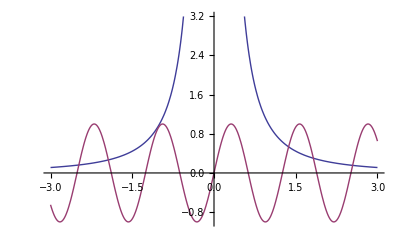

-Graphics3D-

```mathematica
y[x_]:=1/x^2
z [x_]:=Sin[5x]
Plot[{{y[x]},{z[x]}},{x,-3,3}]

RevolutionPlot3D[{{y[t]},{z[t]}},{t,-1.177,1.177}, RevolutionAxis->"x",Boxed->True,Axes->True]
```